```mathematica
λ=0.002;
α=0.15;
β=1;
c=1;
k=1000;
A0=1;
W0=100;
Wps0=1;
Wnsm=1;
Ws0=1;
Wc0=1;
ext=0.1;
αicp=0.001;
αacp=0.001;
αrcp=0.001;
αfc=0.15;
αrc=0.15;
tmax=100;
```

```mathematica
Wrs=αfc*Wic+αrc*Wrc;
Wps=Wps0;
Wns=Wnsm(1-Exp[-W[t]/W0]);
Ws=Wrs+Wps+Wns;

Wic=αicp P[t];
Wac=αacp P[t];
Wrc=αrcp P[t];
Wc=Wic+Wac+Wrc;

A=β Exp[Ws/Ws0-Wc/Wc0]+c;
```

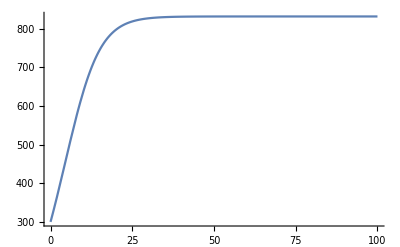

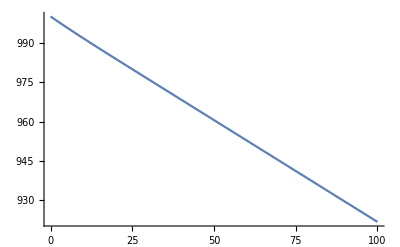

-Graphics-

```mathematica
eqns={
P'[t]==λ P[t](1-P[t]/(k(1-Exp[-A/A0]))),
W'[t]==ext-Wns+α Wac
};
init={
P[0]==300,
W[0]==1000
};
sol=NDSolve[eqns~Join~init,{P,W},{t,0,tmax}];
Plot[P[t]/.sol,{t,0,tmax},PlotRange->All]
Plot[W[t]/.sol,{t,0,tmax},PlotRange->All]
```